Use ellipses for level curves - they are easy to read.
Use something more complex for the constraint
You need to rotate them in space.

{0.707107,1.41421,2.12132,2.82843}

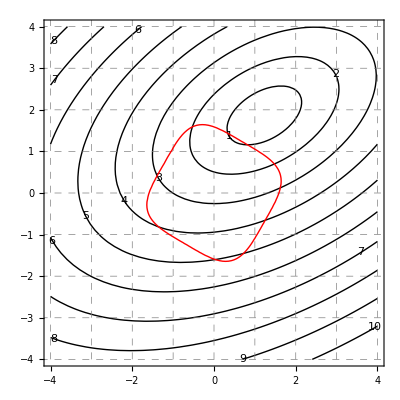

```mathematica
Table[n*Sqrt[2]/2.,{n,1,4}]
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
G[x_,y_]=x^4+y^4;
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=Pi/6;
gAngle=Pi/3;
levelCurves=ContourPlot[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,{x,-4,4},{y,-4,4},
Contours->10,
ContourStyle->{Thick},
ContourLabels->(Text[#3,{#1,#2},Background->White]&),
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],
ContourShading->False];
constraint=ContourPlot[G[{x,y}.rotateX[gAngle],{x,y}.rotateY[gAngle]]==4,{x,-4,4},{y,-4,4},
ContourStyle->{Red,Thick}];
Show[levelCurves,constraint]
```

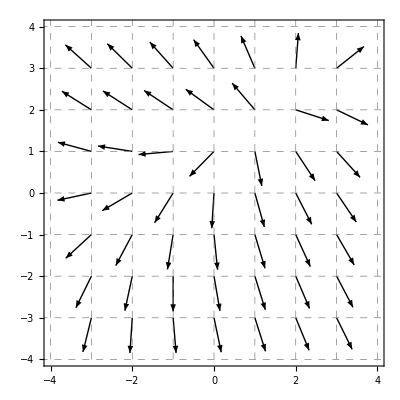

```mathematica
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=Pi/6;
gAngle=Pi/3;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};

gradVects=VectorPlot[grad[x,y]/Sqrt[grad[x,y].grad[x,y]],{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["vectors1.eps",gradVects]
```

vectors1.eps

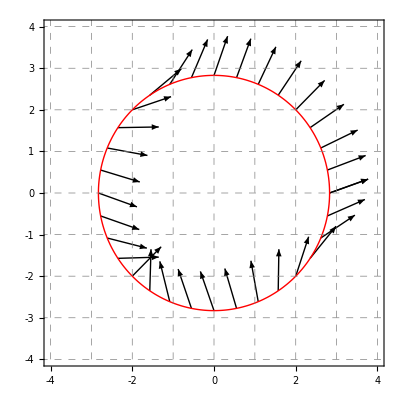

```mathematica
F[x_,y_]=Sqrt[(x-2)^2+3(y-1)^2];
F[x_,y_]=x^3+y^3+3x y;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=0*Pi/4;
gAngle=0*Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVector=Show[gradVects,curve,GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Export["curveVectors1.pdf",curveVector]
```

curveVectors1.pdf

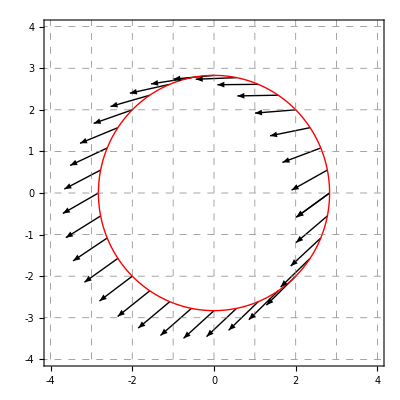

```mathematica
F[x_,y_]=(x-3)^2+3(y-4)^2;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=-Pi/4;
gAngle=7Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVector=Show[gradVects,curve,GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Export["curveVectors2.pdf",curveVector]
```

curveVectors2.pdf

```mathematica
F[x_,y_]=(x-3)^2+3(y-4)^2;
x[t_]=Sqrt[2]2Cos[t];
y[t_]=Sqrt[2]2Sin[t];
rotateX[theta_]={Cos[theta],Sin[theta]};
rotateY[theta_]={-Sin[theta],Cos[theta]};
fAngle=-Pi/4;
gAngle=7Pi/4;
grad[x_,y_]={D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,x],D[F[{x,y}.rotateX[fAngle],{x,y}.rotateY[fAngle]] ,y]};
curve=ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotStyle->{Thick,Red}];
gradVects=Graphics[Table[Arrow[{{x[t],y[t]},{x[t],y[t]}+grad[x[t],y[t]]/Sqrt[grad[x[t],y[t]].grad[x[t],y[t]]]}],{t,0,2Pi,2Pi/32}]];
curveVector=Show[gradVects,curve,GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},PlotRange->{{-4,4},{-4,4}}]
```